```mathematica
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d lnum ;       
   1  2 3 4  5  6  ; *)
```

```mathematica
zero3D[p_?NumberQ,z0_?NumberQ,dnum_?NumberQ,Lnum_?NumberQ]:=Block[
{sol,s,z,v,r,θ},
sol=NDSolve[
{z'[s]==Sin[θ[s]],
r'[s]==Cos[θ[s]],
v'[s]==-2*Pi*z[s]*r[s]*Cos[θ[s]],
θ'[s]==p-z[s] -  Sin[θ[s]] / r[s],

v[ϵ]==ϵ,
r[ϵ]== ϵ,
θ[ϵ]== ϵ,
z[ϵ]==z0},

{z[s],v[s],θ[s],r[s]},{s,ϵ,Lnum}
];

(*conditions de bords*)
{z[s],v[s]-A,θ[s]-θY,r[s] - dnum}/.sol[[1]]/.s->Lnum
]
```

```mathematica
θY=0.1;
ϵ=10^-8;
grsdepart={0.1,0.07170979026585593,0.18375456797317163,-0.05081880154450663,0.9567616804836284,0.9585198853673327};
listeGRS={grsdepart}; 
dernierpointtrouve=listeGRS[[-1]];
A=dernierpointtrouve[[2]];
{papprox,z0approx,dapprox,Lapprox}=grsdepart[[{3,4,5,6}]];
(* c'est la matrice de sortie *)
```

```mathematica
zero3D[papprox,z0approx,dapprox,Lapprox]
```

{-5.84265×10^-18,-1.38778×10^-17,-1.38778×10^-17,-4.44089×10^-16}

```mathematica
fr=FindRoot[zero3D[p,z0,dnum,Lnum],{p,papprox},{z0,z0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];
```

```mathematica
Print[{p,z0,dnum,Lnum}/.fr];
```

{0.183755,-0.0508188,0.956762,0.95852}

fonction du tir1

```mathematica
θY=0.1;
tailledupas=0.1;
imax=600;
grsdepart={0.1,0.07170979026585593,0.18375456797317163,-0.05081880154450663,0.9567616804836284,0.9585198853673327};
listeGRS={grsdepart}; 
{papprox,z0approx,dapprox,Lapprox}=grsdepart[[{3,4,5,6}]];
A=grsdepart[[2]]+ tailledupas /5;
fr=FindRoot[zero3D[p,z0,dnum,Lnum],{p,papprox},{z0,z0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];

(* je verifie si c est une bonne solution *)
erreur=Total[Abs[zero3D[p/.fr,z0/.fr,dnum/.fr,Lnum/.fr]]];
(* θY  A  q  Subscript[y, 0] d lgc ;   
    1  2  3  4  5  6  ; *)
AppendTo[listeGRS,{θY,A,p,z0,dnum,Lnum}/.fr];
Print[erreur];
LastPtFind=listeGRS[[-1]];
Last2PtFind=listeGRS[[-2]];
Print["Last2PtFind : ",Last2PtFind];
Print["LastPtFind : ",LastPtFind];
```

8.30717×10^-16

Last2PtFind : {0.1,0.0717098,0.183755,-0.0508188,0.956762,0.95852}

LastPtFind : {0.1,0.0917098,0.165527,-0.055623,1.03602,1.03796}

zero3D2 (s)

```mathematica
zero3D2[A_?NumberQ,p_?NumberQ,z0_?NumberQ,dnum_?NumberQ,Lnum_?NumberQ]:=Block[
{sol,s,y,a,x,θ},
sol=NDSolve[
{z'[s]==Sin[θ[s]],
r'[s]==Cos[θ[s]],
v'[s]==-2*Pi*z[s]*r[s]*Cos[θ[s]],
θ'[s]==p-z[s] -  Sin[θ[s]] / r[s],

v[ϵ]==ϵ,
r[ϵ]== ϵ,
θ[ϵ]== ϵ,
z[ϵ]==z0},

{z[s],v[s],θ[s],r[s]},{s,ϵ,Lnum}
];

(*conditions de bords*)
{z[s],v[s]-A,θ[s]-θY,r[s] - dnum,
u.{(A - Aapprox),(p - papprox),(z0 - z0approx),(dnum - dapprox),(Lnum - Lapprox)}}/.sol[[1]]/.s->Lnum
]
```

```mathematica
Testcase
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d lnum ;       
   1  2 3 4  5  6  ; *)
```

```mathematica
{AAV,pAV,z0AV,dAV,LAV}=LastPtFind[[{2,3,4,5,6}]];
{AAV2,pAV2,z0AV2,dAV2,LAV2}=Last2PtFind[[{2,3,4,5,6}]];
tailledupas=0.1;
u=Normalize[{AAV-AAV2,pAV-pAV2,z0AV-z0AV2,dAV-dAV2,LAV-LAV2}];
{Aapprox,papprox,z0approx,dapprox,Lapprox}={AAV,pAV,z0AV,dAV,LAV}+u*tailledupas;
Print[Aapprox,"/",papprox,"/",z0approx,"/",dapprox,"/",Lapprox];
Print[u]
```

0.0938373/0.0900697/-0.0879696/1.50661/1.50985

{0.121275,-0.0931042,-0.0516269,0.696753,0.698923}

```mathematica
fr2=FindRoot[zero3D2[A,p,z0,dnum,Lnum],{A,Aapprox},{p,papprox},{z0,z0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];
```

```mathematica
erreur=Total[Abs[zero3D2[A/.fr2, p/.fr2, z0/.fr2, dnum/.fr2,Lnum/.fr2]]];
Which[
erreur<10^-6,
(* θY  A  q  Subscript[y, 0] d Bo ;   
    1  2  3  4  5  6  ; *)
AppendTo[listeGRS,{θY,A,p,z0,dnum,Lnum}/.fr2];
,
erreur≥10^-6,
Print[erreur];
]
LastPtFind=listeGRS[[-1]];
Last2PtFind=listeGRS[[-2]];
Print["Last2PtFind : ",Last2PtFind];
Print["LastPtFind : ",LastPtFind];
```

Fonction du tir mieux

```mathematica
Do[
{AAV,pAV,z0AV,dAV,LAV}=LastPtFind[[{2,3,4,5,6}]];
{AAV2,pAV2,z0AV2,dAV2,LAV2}=Last2PtFind[[{2,3,4,5,6}]];
u=Normalize[{AAV-AAV2,pAV-pAV2,z0AV-z0AV2,dAV-dAV2,LAV-LAV2}];
(*Print["u:",u];*)

Label[begin];
{Aapprox,papprox,z0approx,dapprox,Lapprox}={AAV,pAV,z0AV,dAV,LAV}+u*tailledupas;
(*Print["previous:",{Vapprox,papprox,z0approx,dapprox}];*)
fr2=FindRoot[zero3D2[A,p,z0,dnum,Lnum],{A,Aapprox},{p,papprox},{z0,z0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];

(* je verifie si c est une bonne solution *)
erreur=Total[Abs[zero3D2[A/.fr2, p/.fr2, z0/.fr2, dnum/.fr2,Lnum/.fr2]]];

Which[
erreur<10^-6,
AppendTo[listeGRS,{θY,A,p,z0,dnum,Lnum}/.fr2];
LastPtFind=listeGRS[[-1]];
Last2PtFind=listeGRS[[-2]];
(*Print["LastPtFind:",{V2,p,z0,d}/.fr];*)
,

erreur≥10^-6,
(* did not converge : probleme*)
tailledupas=tailledupas*0.8;
If[tailledupas<10^-6,Print["Stop !!!"];Abort[]];
Print[i," erreur = ",erreur," nouvelle taille du pas : ",tailledupas];
Goto[begin]
,

True,Print["Je ne comprends pas erreur : ",erreur]
];

If[Mod[i,50]==0,
Print[i,"/",imax];
]
,{i,1,imax}]
```

50/600

100/600

150/600

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

200/600

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

250/600

300/600

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

323 erreur = 0.00755978 nouvelle taille du pas : 0.08

350/600

400/600

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

422 erreur = 0.00180933 nouvelle taille du pas : 0.064

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

422 erreur = 0.0000313462 nouvelle taille du pas : 0.0512

423 erreur = 0.0119081 nouvelle taille du pas : 0.04096

450/600

500/600

550/600

600/600

```mathematica
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d lnum ;       
   1  2 3 4  5  6  ; *)
data=Abs[listeGRS[[All,{2,5}]]];

DeleteFile[NotebookDirectory[]<>"3dsliding.data"];
Save[NotebookDirectory[]<>"3dsliding.data",{
listeGRS,data
}];
Print[FileByteCount[(NotebookDirectory[]<>"3dsliding.data")]/1024/1024.," Mo"]
```

0.0947886 Mo

0.0947886 Mo

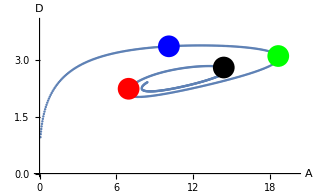

```mathematica
Get[(NotebookDirectory[]<>"3dsliding.data")];
Print[FileByteCount[(NotebookDirectory[]<>"3dsliding.data")]/1024/1024.," Mo"]
plotnumerique=ListPlot[data,AxesLabel-> {Style["A",FontSize->22],Style["D",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,AxesStyle->Black];
Datadots=data[[{115,202,325,420}]];
plotdot2=ListPlot[Datadots,Epilog->{PointSize[0.05],Riffle[{Blue,Green,Red,Black},Point/@Datadots]}];
Show[plotnumerique,plotdot2,AxesStyle->Black,Epilog->{PointSize[0.05],Riffle[{Blue,Green,Red,Black},Point/@Datadots]},PlotRange->{{0,20},{0,4}}]
```

c’est le plot

Aplot:14.4024/pplot:-0.517708/z0plot:-4.17164/dplot:2.78918/Lplot:5.7989

{z[s]→InterpolatingFunction[…][s],v[s]→InterpolatingFunction[…][s],θ[s]→InterpolatingFunction[…][s],r[s]→InterpolatingFunction[…][s]}

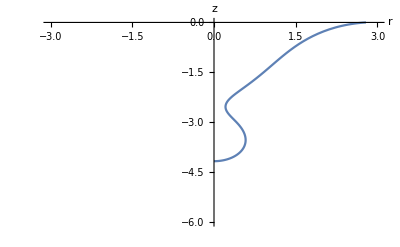

{y→InterpolatingFunction[…],a→InterpolatingFunction[…],x→InterpolatingFunction[…],θ→InterpolatingFunction[…]}

```mathematica
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d lnum ;       
   1  2 3 4  5  6  ; *)
(*test part of plot*)
Datadots=data[[{115,202,325,420}]];
listplot=listeGRS[[420]];
{Aplot,pplot,z0plot,dplot,Lplot}=listplot[[{2,3,4,5,6}]];
Print["Aplot:",Aplot,"/pplot:",pplot,"/z0plot:",z0plot,"/dplot:",dplot,"/Lplot:",Lplot]
solforme=NDSolve[{
z'[s]==Sin[θ[s]],
r'[s]==Cos[θ[s]],
v'[s]==-2*z[s]*r[s]*Cos[θ[s]],
θ'[s]==pplot-z[s] -  Sin[θ[s]] / r[s],

v[ϵ]==ϵ,
r[ϵ]== ϵ,
θ[ϵ]== ϵ,
z[ϵ]==z0plot},

{z[s],v[s],θ[s],r[s]},{s,ϵ,Lplot}
][[1]]
ParametricPlot[{r[s],z[s]}/.solforme,{s,0,Lplot},
AxesLabel-> {Style["r",FontSize->22],Style["z",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotRange->{{-3,3},{-6,0}},AxesStyle->Black]
(*Plot[Evaluate[θ[s]]/.solforme,{s,0,Lplot},AxesLabel-> {Style["s",FontSize->22],Style["θ",FontSize->22]},LabelStyle->{FontSize->22}]*)
{y->InterpolatingFunction[…],a->InterpolatingFunction[…],x->InterpolatingFunction[…],θ->InterpolatingFunction[…]}
```

```mathematica
(*real part of plot*)

Clear[splot,splot2]
positiondots={115,202,325,420};
j=1;
Color={Blue,Green,Red,Black};
```

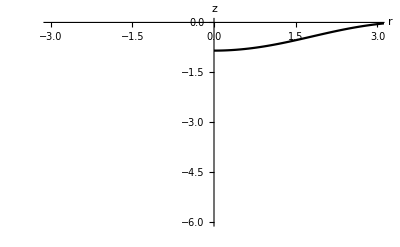
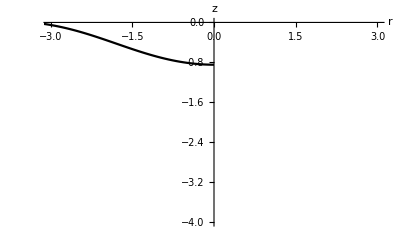
```mathematica
Do[
number=positiondots[[j]];
listplot=listeGRS[[number]];
{Aplot,pplot,z0plot,dplot,Lplot}=listplot[[{2,3,4,5,6}]];
Print["plot:",Aplot,"/",pplot,"/",z0plot,"/",dplot,"/",Lplot,"/",Color[[j]],"/",number];
solforme=NDSolve[{
z'[s]==Sin[θ[s]],
r'[s]==Cos[θ[s]],
v'[s]==-2*z[s]*r[s]*Cos[θ[s]],
θ'[s]==pplot-z[s] -  Sin[θ[s]] / r[s],

v[ϵ]==ϵ,
r[ϵ]== ϵ,
θ[ϵ]== ϵ,
z[ϵ]==z0plot},

{z[s],v[s],θ[s],r[s]},{s,ϵ,Lplot}
][[1]];
splot[j]=ParametricPlot[{θ[s]}/.solforme,{s,0,Lplot},
AxesLabel-> {Style["r",FontSize->22],Style["z",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotRange->{{-3,3},{-6,0}},AxesStyle->Black,PlotStyle->Color[[j]]];
splot2[j]=ParametricPlot[{-r[s],z[s]}/.solforme,{s,0,Lplot},
AxesLabel-> {Style["r",FontSize->22],Style["z",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotRange->{{-3,3},{-4,0}},AxesStyle->Black,PlotStyle->Color[[j]]];
,
{j,1,4}]
-Graphics-
-Graphics-
5
```

plot:10.1109/-0.227636/-0.847205/3.34702/3.4698/RGBColor[0, 0, 1]/115

plot:18.6632/-0.556911/-2.06951/3.09172/3.85213/RGBColor[0, 1, 0]/202

plot:6.96323/-0.355988/-3.43422/2.23051/4.86882/RGBColor[1, 0, 0]/325

plot:14.4024/-0.517708/-4.17164/2.78918/5.7989/GrayLevel[0]/420

-Graphics-

-Graphics-

5

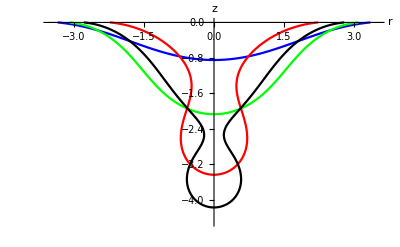

```mathematica
tb3D=Table[splot[i],{i,1,4,1}];
tb3D2=Table[splot2[i],{i,1,4,1}];
Show[tb3D,tb3D2,PlotRange->{{-3.5,3.5},{-4.5,0}}]
```

c’est les donnes calcul avant 3D bvp

```mathematica
Data2={{0.1,0.07170979026585593,0.1837545624775352,-0.05081880492310522,0.9567617003179247},{0.1,0.08,0.17550818641195767,-0.05289274112643068,0.9912818700846068},{0.1,0.09239038487484702,0.16499625051421327,-0.05577543382952381,1.0384979572966906},{0.1,0.10601563612836441,0.15529498771067918,-0.05870445760011871,1.0855497350751104},{0.1,0.12091410021938245,0.14631223258499862,-0.06167795095841449,1.1323546915352722},{0.1,0.13711913727651717,0.13796780853155943,-0.06469438650022412,1.1788400289438365},{0.1,0.154657320687795,0.1301927597968708,-0.06775216537033611,1.2249362847314278},{0.1,0.17354770215187534,0.12292760189699382,-0.07084956493522372,1.270576991342977},{0.1,0.19380140355177153,0.11612083225015198,-0.07398471105547547,1.315698664402234},{0.1,0.2154213811338778,0.1097276749626569,-0.07715556822712735,1.3602410472017203},{0.1,0.2384023170963925,0.1037090293601809,-0.08035994843458481,1.4041475591758792},{0.1,0.2627308142047802,0.09803058835856424,-0.08359553035666083,1.447365799799687},{0.1,0.2883857757954715,0.09266210604977512,-0.08685989082950643,1.489848075754477},{0.1,0.3153389620630332,0.08757678685530695,-0.09015054181527185,1.5315518954158158},{0.1,0.3435557541470246,0.0827507782194785,-0.09346497024103265,1.5724403487536445},{0.1,0.37299600459049675,0.07816275042919571,-0.09680067988039444,1.6124823831318507},{0.1,0.4036149956570417,0.07379354759443864,-0.1001552298106197,1.6516529218804161},{0.1,0.435364431795005,0.0696258983565621,-0.10352626843582584,1.6899328335751653},{0.1,0.4681933924811408,0.06564417586307428,-0.10691156439286671,1.7273087862591445},{0.1,0.502049279837408,0.061834197325892626,-0.1103090284248598,1.7637729517472143},{0.1,0.5368786676227261,0.05818305635257021,-0.11371673017278844,1.7993226275117622},{0.1,0.5726280753037238,0.05467898181947964,-0.1171329071892132,1.8339597690690088},{0.1,0.6092445651879348,0.051311217048741926,-0.1205559739446188,1.8676905430804382},{0.1,0.6466763493145375,0.048069917465120175,-0.1239845164260846,1.9005247466490889},{0.1,0.6848731846287612,0.04494606107915006,-0.12741729052771864,1.9324753186905805},{0.1,0.7237867125862999,0.041931371019974996,-0.13085321570338976,1.9635578270160687},{0.1,0.7633707080291694,0.039018245572153255,-0.13429135872968684,1.9937899782468307},{0.1,0.8035812077477393,0.03619969838794266,-0.1377309324365914,2.023191212485412},{0.1,0.8443766271987557,0.03346930320068316,-0.14117127720759695,2.051782275469407},{0.1,0.8857177866926815,0.030821144796192315,-0.14461185024589646,2.0795848727931716},{0.1,0.9275679338507536,0.028249778733123038,-0.1480522198806235,2.1066213110873733},{0.1,0.969892567314364,0.025750175372445578,-0.15149203082627055,2.132914424864565},{0.1,1.0126595627459336,0.023317705930559426,-0.15493102447754026,2.1584870613125533},{0.1,1.0558389459758677,0.020948094585546917,-0.15836900892786226,2.1833620829103273},{0.1,1.099402825839073,0.018637391615414736,-0.16180585417995924,2.2075621640647602},{0.1,1.143325281712443,0.01638194580747777,-0.1652414833925092,2.2311096637932053},{0.1,1.187582242604246,0.014178380078201339,-0.16867586977939222,2.254026534212006},{0.1,1.232151394248612,0.012023566356792673,-0.17210901507608017,2.2763342001178186},{0.1,1.2770120286585427,0.009914606683952078,-0.17554096047273662,2.298053561671539},{0.1,1.3221449556461355,0.007848813266647651,-0.17897177218847815,2.3192049105081116},{0.1,1.3675323893612723,0.0058236911798635665,-0.18240153842982537,2.3398079089786434},{0.1,1.4131578459784029,0.003836922476976201,-0.18583036523458443,2.3598815712126497},{0.1,1.459006043500632,0.0018863523345211146,-0.18925837619266764,2.379444260380931},{0.1,1.505062819193526,-0.00003002568624291185,-0.19268570148651742,2.398513668864428},{0.1,1.5513150375222837,-0.0019140803211302026,-0.19611248161746006,2.4171068357916834},{0.1,1.597750502649111,-0.003767556370337234,-0.19953886336153948,2.4352401769184877},{0.1,1.64435792489341,-0.00559207527157779,-0.20296499839660567,2.4529293986387395},{0.1,1.691126791919691,-0.0073891583880102505,-0.20639104056482566,2.4701896600313584},{0.1,1.7380473473567024,-0.009160225933374726,-0.20981714527815992,2.4870354914930743},{0.1,1.7851105216756595,-0.010906606928076067,-0.21324346812580508,2.503480838013482},{0.1,1.8323078789722416,-0.012629546173696505,-0.2166701639273967,2.5195390789698826},{0.1,1.8796315671934554,-0.014330210473841766,-0.2200973868025132,2.5352230500394084},{0.1,1.927074274920855,-0.0160096948120631,-0.22352528713966863,2.5505450585329967},{0.1,1.974629187308671,-0.017669027393787274,-0.22695401357019224,2.565516910860497},{0.1,2.0222899493748,-0.019309174615139778,-0.23038371140411307,2.5801499293075545},{0.1,2.070050630656293,-0.020931045541849113,-0.23381452249041243,2.5944549731170796},{0.1,2.1179056930603757,-0.02253549601883243,-0.23724658496769385,2.608442458345575},{0.1,2.165849961343091,-0.024123332443010095,-0.2406800330801167,2.622122377200698},{0.1,2.2138785957938416,-0.02569531516149797,-0.24411499750354387,2.635504317420192},{0.1,2.261987068314525,-0.027252161889959242,-0.24755160338642435,2.6485974774280887},{0.1,2.3101711358710357,-0.028794550189465674,-0.25098997538123946,2.661410695735329},{0.1,2.3584268278019227,-0.03032312080291772,-0.254430228651812,2.67395243993557},{0.1,2.4067504167759206,-0.03183847959657797,-0.25787247797376356,2.6862308553852694},{0.1,2.4551384065917,-0.03334120010763881,-0.2613168330878947,2.6982537621172424},{0.1,2.50358751454121,-0.034831825618120135,-0.2647633997210739,2.7100286736110597},{0.1,2.552094653547882,-0.036310873580297824,-0.26821227015846344,2.7215628249536037},{0.1,2.6006569292577275,-0.03777882759891202,-0.27166356142709386,2.732863131561538},{0.1,2.6492716111616477,-0.03923615379105986,-0.2751173582841667,2.743936281806027},{0.1,2.697936131459368,-0.040683292600149766,-0.2785737513213244,2.7547886971419913},{0.1,2.7466480714179595,-0.04212066265451497,-0.2820328275960567,2.7654265563921503},{0.1,2.795405151384522,-0.04354866210521021,-0.2854946707499448,2.7758558067581878},{0.1,2.844205221500631,-0.04496766986640035,-0.28895936112482973,2.7860821742752884},{0.1,2.893046253116669,-0.046378046767978263,-0.2924269758800331,2.796111173748484},{0.1,2.9419263308481574,-0.047780136627465,-0.29589758910963854,2.8059481181944403},{0.1,2.990843642029483,-0.0491742674262315,-0.29937127345564457,2.81559814311862},{0.1,3.0397964811383464,-0.05056075146810512,-0.3028480956672557,2.825066161356161},{0.1,3.0887832288111507,-0.051939887547354936,-0.3063281210814846,2.834356941015103},{0.1,3.1378023535659434,-0.05331196046659029,-0.3098114150203788,2.843475076905993},{0.1,3.186852406715976,-0.0546772428151515,-0.31329803666499567,2.852424997006346},{0.1,3.2359320154301368,-0.05603599503770781,-0.31678804432355834,2.861210977383721},{0.1,3.285039878625632,-0.057388466285824745,-0.32028149403889694,2.8698371464166432},{0.1,3.3341747625718536,-0.05873489503732737,-0.3237784396953336,2.878307491171999},{0.1,3.383335495239596,-0.06007550989742597,-0.32727893266476515,2.886625872723259},{0.1,3.4325209675559947,-0.061410529320993765,-0.3307830239803871,2.894796002167825},{0.1,3.481730123987398,-0.06274016317635793,-0.334290761094522,2.902821480630038},{0.1,3.530961962243629,-0.06406461261901196,-0.3378021902960868,2.910705786881706},{0.1,3.5802155296503706,-0.06538407066362247,-0.341317356194212,2.918452285371787},{0.1,3.629489920293746,-0.06669872260291526,-0.34483630180147395,2.9260642308706157},{0.1,3.678784272344171,-0.06800874640120028,-0.34835906861220567,2.933544772889284},{0.1,3.72809776421387,-0.06931431332458624,-0.35188569654776847,2.9408969687409843},{0.1,3.7774296164430745,-0.07061558739589809,-0.3554162246465418,2.948123759856892},{0.1,3.826779084481536,-0.07191272685787951,-0.35895069034295285,2.9552280082608164},{0.1,3.8761454593167937,-0.07320588384070426,-0.3624891299531755,2.9622124831114967},{0.1,3.925528065010355,-0.07449520478633001,-0.3660315786765142,2.969079867464225},{0.1,3.97492625884217,-0.07578083115804543,-0.3695780675923126,2.975832749157212},{0.1,4.024339419468774,-0.07706289863393401,-0.3731286343130822,2.9824736918211356},{0.1,4.073766965905209,-0.07834153746681467,-0.3766833106756326,2.9890050964275465},{0.1,4.123208335564809,-0.07961687448676259,-0.3802421267410807,2.995429348190835},{0.1,4.172662993003251,-0.08088903153328122,-0.38380511298975195,3.00174874699797},{0.1,4.222130426551412,-0.08215812619038483,-0.3873722991387075,3.007965524400673},{0.1,4.271610146366614,-0.08342427216909738,-0.39094371310237047,3.014081852646678},{0.1,4.321101685577696,-0.08468757893740454,-0.3945193846401219,3.0200998269695694},{0.1,4.37060459647854,-0.08594815251150034,-0.39809934085860793,3.0260214914984016},{0.1,4.420118450930545,-0.08720609532287261,-0.40168360885369164,3.0318488290526577},{0.1,4.469642839102377,-0.08846150642700497,-0.4052722151919468,3.037583765654926},{0.1,4.519177368561238,-0.08971448165229437,-0.40886518595391097,3.043228172526309},{0.1,4.56872166660991,-0.09096511383226989,-0.41246254647251007,3.04878384009697},{0.1,4.618275365418215,-0.09221349296778668,-0.4160643206732283,3.054252603379181},{0.1,4.667838124959022,-0.09345970553389438,-0.4196705362292216,3.059636133952078},{0.1,4.717409613282655,-0.09470383605283439,-0.42328121622641873,3.064936110955892},{0.1,4.766989512906671,-0.09594596621734715,-0.4268963848476435,3.0701541593419797},{0.1,4.816577519226322,-0.09718617524339507,-0.4305160660066817,3.075291859673671},{0.1,4.866173339917131,-0.09842453997467623,-0.43414028338231503,3.0803507496042526},{0.1,4.915776694356484,-0.09966113498173218,-0.4377690604503844,3.0853323252898472},{0.1,4.965387313076504,-0.10089603265630563,-0.4414024205149318,3.0902380427413583},{0.1,5.015004937246293,-0.10212930330122139,-0.445040386738448,3.0950693191181538},{0.1,5.064629317112954,-0.10336101557140673,-0.4486829798734949,3.099827546582468},{0.1,5.114260215085779,-0.10459123537897076,-0.4523302258106919,3.1045140520096535},{0.1,5.163897400464286,-0.10582002754969465,-0.4559821458871193,3.109130153971133},{0.1,5.213540652473156,-0.10704745479808579,-0.4596387630970306,3.113677124695633},{0.1,5.263189758556087,-0.10827357762246587,-0.46330010304347397,3.118156203327649},{0.1,5.312844514708392,-0.10949845598161766,-0.4669661864185905,3.122568594999706},{0.1,5.362504720268128,-0.11072214844696046,-0.47063702976484306,3.1269155259295345},{0.1,5.4121701919599525,-0.11194471089364594,-0.47431266381435194,3.1311980689575227},{0.1,5.46184073158752,-0.11316619598497947,-0.4779930772356408,3.1354175535677156},{0.1,5.511516187596962,-0.11438666197257485,-0.48167835200952613,3.1395747416280226},{0.1,5.561196378523324,-0.11560615873713215,-0.48536848285999334,3.143670857858686},{0.1,5.610881141277546,-0.1168247372655538,-0.4890634927697297,3.1477069410720735},{0.1,5.660570318444453,-0.11804244731321763,-0.4927634048220786,3.151684004452518},{0.1,5.710263758232701,-0.11925933745669261,-0.49646824223205854,3.155603036336892},{0.1,5.759961314235762,-0.1204754551395233,-0.5001780283619283,3.1594650009504828},{0.1,5.8096628452043335,-0.12169084671612256,-0.5038927867362583,3.163270839116245},{0.1,5.859368214829531,-0.12290555749386703,-0.5076125410565118,3.1670214689385956},{0.1,5.909077291871055,-0.12411963186289644,-0.5113373153792684,3.1707177818350707},{0.1,5.958789948736201,-0.12533311312726217,-0.5150671430285022,3.1743606503937305},{0.1,6.00850606512079,-0.12654604139240605,-0.5188020508266367,3.1779508938231396},{0.1,6.058225518815749,-0.12775846256611,-0.5225420380259885,3.1814894199004615},{0.1,6.107948195662812,-0.12897042165683834,-0.5262871012340862,3.1849770679381266},{0.1,6.157673989273513,-0.13018193864429034,-0.5300373914864401,3.1884144453920364},{0.1,6.2074027863341765,-0.13139307353380114,-0.5337928003047728,3.1918025514735886},{0.1,6.257134486811516,-0.1326038566957472,-0.5375534047426498,3.195142046142784},{0.1,6.306868992710936,-0.13381432649399533,-0.541319236287375,3.1984336307534593},{0.1,6.356606201993891,-0.13502451783808117,-0.5450903063695165,3.2016781234056175},{0.1,6.4063460132517855,-0.13623446479742543,-0.5488665884237671,3.2048764146363915},{0.1,6.456088357121309,-0.13744420918317368,-0.5526482289182733,3.208028729508153},{0.1,6.505833134732429,-0.13865378282346824,-0.5564351959200312,3.211135975631663},{0.1,6.555580261252008,-0.13986321996835477,-0.5602275169753931,3.2141988129106407},{0.1,6.605329654288779,-0.14107255428153714,-0.5640252199682834,3.217217886337536},{0.1,6.655081242353366,-0.14228182548695253,-0.5678283988749622,3.220193603557848},{0.1,6.7048349312896045,-0.14349105391639835,-0.5716369526789088,3.2231270220837347},{0.1,6.754590654689271,-0.14470027708427352,-0.5754509737050981,3.2260185273438196},{0.1,6.804348339543059,-0.145909526613687,-0.5792704921629555,3.2288687087498316},{0.1,6.854107913030425,-0.1471188284922935,-0.5830955418401139,3.2316781787832465},{0.1,6.903869309868218,-0.14832821911292246,-0.5869261313869882,3.2344474730821355},{0.1,6.953632464507701,-0.1495377321475237,-0.5907623222483422,3.2371770825029467},{0.1,7.003397310805211,-0.15074739331716536,-0.5946041319018767,3.239867594441804},{0.1,7.053163788339271,-0.15195723755627055,-0.5984516011932102,3.242519480098603},{0.1,7.1029318313662975,-0.15316728299681387,-0.6023047439982684,3.245133375987477},{0.1,7.152701383477275,-0.1543775635290015,-0.6061636016715338,3.247709723410274},{0.1,7.202472387193707,-0.15558810740791917,-0.6100282070930266,3.2502490157922823},{0.1,7.252244786689473,-0.15679894255065943,-0.6138985936266527,3.252751735864371},{0.1,7.302018527681917,-0.15801009654985126,-0.6177747951267457,3.255218355913058},{0.1,7.351793557374146,-0.15922159668791047,-0.6216568459486005,3.2576493380247387},{0.1,7.401569824399564,-0.16043346995091176,-0.6255447809589316,3.2600451343222967},{0.1,7.451347278768543,-0.16164574304209747,-0.6294386355462452,3.262406187194637},{0.1,7.5011258718170994,-0.16285844239500208,-0.6333384456310073,3.26473292951991},{0.1,7.550905556076791,-0.1640715944236166,-0.6372442443630332,3.2670257920379253},{0.1,7.600686284578193,-0.16528521969812962,-0.6411560238715834,3.2692852864839077},{0.1,7.650468014654689,-0.1664993538972145,-0.6450739171010396,3.2715116020185615},{0.1,7.700250701011648,-0.16771401770516992,-0.6489979139026234,3.273705248690754},{0.1,7.750034299188465,-0.16892923662296325,-0.6529280520493921,3.2758666574528235},{0.1,7.799818770463391,-0.17014503532942146,-0.6568643726728192,3.2779961390785974},{0.1,7.849604072146256,-0.1713614420443799,-0.6608069724722151,3.280094004175258},{0.1,7.899390168508825,-0.17257848098157777,-0.6647557961457937,3.282160699155481},{0.1,7.949177014877018,-0.17379616867381256,-0.6687108971515155,3.2841967059292436},{0.1,7.998964575730606,-0.1750145273449533,-0.6726723511820424,3.286202257524742},{0.1,8.048752815671243,-0.17623360358250342,-0.676640180641695,3.2881776803864184},{0.1,8.098541697383196,-0.17745338779383465,-0.680614436109858,3.2901233436828536},{0.1,8.148331185083975,-0.17867393437820542,-0.6845951712034629,3.2920395481089675},{0.1,8.198121243862499,-0.17989526220601432,-0.6885824243523313,3.2939266380824113},{0.1,8.247911841620297,-0.18111738231218455,-0.6925762343065732,3.2957849045119447},{0.1,8.297702944416436,-0.18234032464250297,-0.696576649757723,3.29761466616451},{0.1,8.347494519872738,-0.1835641127783101,-0.7005837166759524,3.299416224243812},{0.1,8.397286536271327,-0.18478877021988466,-0.7045974817165892,3.3011898735958467},{0.1,8.447078962534771,-0.18601432039504256,-0.7086179922306943,3.3029359028368734},{0.1,8.496871770434945,-0.18724078033996236,-0.7126452179202282,3.3046547156441743},{0.1,8.546664923641131,-0.18846819719484548,-0.7166794458264315,3.306346207107944},{0.1,8.596458398987892,-0.18969656540611549,-0.7207204823380851,3.3080110511816807},{0.1,8.646252165876035,-0.19092591935119893,-0.724768461779082,3.309649368411776},{0.1,8.696046195969869,-0.19215628218367486,-0.7288234354575799,3.3112614176649027},{0.1,8.745840461457082,-0.1933876770890538,-0.7328854556429961,3.312847453807294},{0.1,8.795634935326975,-0.1946201271218692,-0.7369545728111245,3.314407722973224},{0.1,8.84542959089583,-0.1958536578315115,-0.7410308326215155,3.3159424827821877},{0.1,8.89522440163481,-0.19708829032156125,-0.7451142961176845,3.3174519609214714},{0.1,8.945019341417398,-0.19832404707755735,-0.7492050236455422,3.3189363825120535},{0.1,8.9948143881465,-0.1995609531729721,-0.7533030041455899,3.3203960425584462},{0.1,9.044609510209373,-0.20079902665341398,-0.7574084144724423,3.321831055759289},{0.1,9.094404686054984,-0.20203829587503763,-0.7615212533163279,3.3232416875378066},{0.1,9.144199891519994,-0.2032787824873753,-0.7656415799186266,3.3246281421661146},{0.1,9.193995102385015,-0.20452050976823974,-0.7697694530742053,3.3259906340675798},{0.1,9.243790289444547,-0.20576349152791876,-0.7739049930239141,3.327329392818134},{0.1,9.293585440016058,-0.20700777097973594,-0.7780481314560055,3.328644598620454},{0.1,9.343380528967096,-0.2082533664599441,-0.7821989709935422,3.3299363990104207},{0.1,9.393175526738153,-0.2095002912957541,-0.7863576297576897,3.3312050717505657},{0.1,9.44297041431043,-0.21074857412430992,-0.7905241429782149,3.332450752846135},{0.1,9.4927651676329,-0.21199824392629218,-0.79469861118181,3.33367356532346},{0.1,9.542559767742375,-0.21324932457248336,-0.7988810276675251,3.3348738004749645},{0.1,9.592354187885313,-0.21450182014167715,-0.8030715298058254,3.3360516118122567},{0.1,9.642148406177926,-0.21575578216472363,-0.807270214254927,3.337207043658923},{0.1,9.691942409373496,-0.21701120498778964,-0.8114769918486453,3.338340503849963},{0.1,9.741736171884295,-0.2182681489113803,-0.8156920478527167,3.339451885088534},{0.1,9.791529668800491,-0.21952661386051783,-0.819915461647354,3.3405414964468183},{0.1,9.841322883818757,-0.22078662804272037,-0.8241472476922855,3.341609498695452},{0.1,9.891115794157471,-0.2220482175333579,-0.8283875113546416,3.342656003645174},{0.1,9.940908379190917,-0.22331140727779863,-0.8326363206728374,3.3436811755945732},{0.1,9.990700618219902,-0.22457622242704495,-0.836893754646224,3.3446851465646814},{0.1,10.040492490721887,-0.22584268810710864,-0.8411598897415133,3.345668055987237},{0.1,10.090283976246713,-0.22711082960916604,-0.8454348039691454,3.34663003968022},{0.1,10.140075054454888,-0.22838067242563168,-0.8497185762559544,3.347571229872968},{0.1,10.189865706045483,-0.22965221850107082,-0.854011254885542,3.348491881375363},{0.1,10.23965590894913,-0.23092553676667238,-0.858312983845652,3.349391878712483},{0.1,10.289445643907419,-0.23220063331629062,-0.8626238128150274,3.3502714682969565},{0.1,10.339234889104864,-0.23347751867844496,-0.866943832298718,3.3511308599212484},{0.1,10.389023629811897,-0.23475628577169816,-0.8712731172680082,3.351969818989172},{0.1,10.438811840001035,-0.2360368825314356,-0.8756117699943974,3.352788830532817},{0.1,10.488599508287683,-0.23731939500348326,-0.8799597994131387,3.353587818237144},{0.1,10.53838660186557,-0.23860379114042207,-0.8843174360466614,3.3543670042760465},{0.1,10.58817310694009,-0.23989012727027859,-0.8886847010760003,3.355126435034206},{0.1,10.637959003385504,-0.24117843106101672,-0.8930616871200694,3.3558662098220884},{0.1,10.68774427104,-0.24246873043715436,-0.8974484883976144,3.356586425022809},{0.1,10.737528887660304,-0.2437610397796993,-0.9018452314799555,3.3572871517208225},{0.1,10.787312837109369,-0.24505541833456618,-0.906251950817429,3.3579685216835093},{0.1,10.837096097007484,-0.24635187837868872,-0.9106687779309591,3.3586305963055567},{0.1,10.886878647026888,-0.24765044862930768,-0.9150958054804859,3.3592735055244893},{0.1,10.936660466552672,-0.2489511595421308,-0.9195331497065757,3.3598972451076645},{0.1,10.98644153500853,-0.250254040457168,-0.9239809076683634,3.360501935458081},{0.1,11.036221824050168,-0.2515591274257728,-0.9284392841437147,3.3610875399625435},{0.1,11.086001327996348,-0.25286643910805623,-0.9329081897108679,3.3616543518019086},{0.1,11.135780018511053,-0.25417601234899057,-0.9373878307981676,3.362202329933898},{0.1,11.185557874429534,-0.25548787839921333,-0.9418783185468669,3.3627315399577613},{0.1,11.235334874492176,-0.2568020688864937,-0.9463797660211728,3.3632420445201276},{0.1,11.285110997270273,-0.2581186158233822,-0.9508922882538694,3.3637339033204636},{0.1,11.334886221153818,-0.2594375516170003,-0.9554160022962557,3.364207173117095},{0.1,11.384660524339738,-0.26075890907988475,-0.9599510272620753,3.364661907735038},{0.1,11.434433897812964,-0.26208270729209243,-0.964497330861092,3.365098307956052},{0.1,11.484206293123728,-0.26340900993421446,-0.9690553477139784,3.3655161105417215},{0.1,11.533977700922817,-0.26473783565115927,-0.9736250459975694,3.365915519636631},{0.1,11.583748089528356,-0.2660692134991112,-0.9782066555439595,3.366296560157708},{0.1,11.63351745381152,-0.26740318982758626,-0.9828001058813246,3.366659303582723},{0.1,11.683285762117618,-0.2687397945873821,-0.9874056244972707,3.3670037768185916},{0.1,11.733052990916047,-0.2700790638372367,-0.9920233464987039,3.3673300113312012},{0.1,11.78281911639993,-0.27142103417528873,-0.9966534094261313,3.3676380366678087},{0.1,11.832584114451247,-0.27276574274754395,-1.0012959533168342,3.367927880004196},{0.1,11.882347960768902,-0.27411322727136844,-1.0059511192031847,3.368199566788801},{0.1,11.932110625573808,-0.27546354232836956,-1.0106191096557833,3.3684529716099774},{0.1,11.981872095564391,-0.27681669992518976,-1.0152999349828324,3.3686884276611893},{0.1,12.031632334775923,-0.2781727488132897,-1.0199938687014216,3.368905734724586},{0.1,12.08139132242343,-0.279531717073864,-1.0247010067571167,3.3691050188358074},{0.1,12.131149029493097,-0.28089366755176326,-1.02942153426399,3.369286172489278},{0.1,12.180905433961748,-0.28225862731773615,-1.0341555652007246,3.369449183335115},{0.1,12.230660501500388,-0.2836266493407914,-1.0389033296811772,3.369594188161231},{0.1,12.280414208194076,-0.28499777095184264,-1.0436649589885851,3.369721122548246},{0.1,12.330166526521992,-0.2863720353358228,-1.0484406158564223,3.3698300008335793},{0.1,12.379917419723377,-0.2877494910372002,-1.0532305562957194,3.3699208488844685},{0.1,12.42966687908038,-0.28913016589487844,-1.0580347502347975,3.3699936086647666},{0.1,12.479414857246615,-0.2905141283771454,-1.0628535562500767,3.3700482082480705},{0.1,12.52916132874045,-0.2919014157704846,-1.0676871096273006,3.370084667089792},{0.1,12.578906263417414,-0.2932920755062785,-1.0725355906148248,3.370103008492052},{0.1,12.628649629768374,-0.2946861566219126,-1.0773991915696395,3.3701031953749823},{0.1,12.67839139560473,-0.29608370745571355,-1.0822781093926184,3.3700851799880063},{0.1,12.728131530271371,-0.29748477123327355,-1.0871725245827453,3.3700490079552465},{0.1,12.777869999672223,-0.2988894024257656,-1.0920826475242027,3.3699945982077724},{0.1,12.827606769643786,-0.3002976562931719,-1.0970086861536934,3.3699219365673225},{0.1,12.877341804239759,-0.3017095860958324,-1.1019508634635982,3.3698309112183757},{0.1,12.927075069189675,-0.30312524493202936,-1.1069093839897495,3.3697215382523122},{0.1,12.976806528477509,-0.3045446876424418,-1.1118844665923138,3.3695937785366485},{0.1,13.026536143561858,-0.30596797096308087,-1.1168763494621476,3.3694475019475805},{0.1,13.076263878458903,-0.30739515261992273,-1.1218852456164814,3.3692827494485957},{0.1,13.125989692318386,-0.30882629236237796,-1.1269114083408927,3.3690993707593426},{0.1,13.175713551765945,-0.3102614369119564,-1.1319550235698173,3.3688974406011747},{0.1,13.22543540421048,-0.31170066829945264,-1.137016443415263,3.368676707924139},{0.1,13.275155220714488,-0.313144025676987,-1.1420958081109096,3.3684373082132044},{0.1,13.324872953883515,-0.314591582359629,-1.1471934165040298,3.3681790708865904},{0.1,13.374588545226935,-0.31604345284844376,-1.152309647056773,3.3679016305783525},{0.1,13.424301978459033,-0.31749960436521185,-1.1574445457076574,3.367605459680783},{0.1,13.474013194166465,-0.3189601530740638,-1.1625984950919046,3.3672902016862887},{0.1,13.523722145175903,-0.3204251677793871,-1.1677717764573734,3.3669557648528423},{0.1,13.573428783221129,-0.3218947188187545,-1.1729646777798428,3.3666020527591605},{0.1,13.623133058746797,-0.32336887811036874,-1.1781774939706904,3.366228964192108},{0.1,13.672834920792058,-0.3248477008682389,-1.1834105427405992,3.3658365304764724},{0.1,13.722534317619388,-0.32633129908586966,-1.1886640990682222,3.365424370548397},{0.1,13.772231195036625,-0.32781973127677566,-1.19393849827117,3.364992502286444},{0.1,13.821925497849131,-0.3293130762336408,-1.1992340652779483,3.3645408044364626},{0.1,13.871617172202443,-0.330811390766817,-1.2045511180663713,3.3640692199899953},{0.1,13.921306153567546,-0.33231480482401293,-1.2098900295062114,3.3635774685547397},{0.1,13.970992385002793,-0.33382337939630036,-1.2152511325337167,3.3630654934502435},{0.1,14.020675797296175,-0.3353372132530257,-1.220634834526848,3.3625329796494725},{0.1,14.07035634058495,-0.3368563712449346,-1.226041412712382,3.3619801106944283},{0.1,14.120033942225927,-0.33838095658098494,-1.2314712916706207,3.3614065621495683},{0.1,14.169708534302316,-0.3399110626888551,-1.2369248603643912,3.3608121708600174},{0.1,14.219380047240715,-0.34144678516018145,-1.2424025152486646,3.3601967698125708},{0.1,14.269048429478822,-0.34298820504751454,-1.2479045148975152,3.3595604499476788},{0.1,14.31871356515263,-0.3445354579153632,-1.253431587851914,3.3589024885410828},{0.1,14.368375397652649,-0.34608863028127007,-1.2589840150570997,3.3582229635220044},{0.1,14.418033847740999,-0.34764782859629717,-1.2645622422338385,3.3575216761388993},{0.1,14.467688833332993,-0.34921316222310195,-1.2701667278031632,3.3567984197643246},{0.1,14.5173402695665,-0.35078474355904904,-1.2757979434166355,3.3560529796152583},{0.1,14.566988068670128,-0.3523626881592982,-1.28145637449136,3.355285132461308},{0.1,14.616632139823716,-0.3539471148662914,-1.2871425207729452,3.3544946463173293},{0.1,14.666272391090601,-0.3555381749697763,-1.2928568575483264,3.3536811856539623},{0.1,14.71590872023237,-0.3571359364526853,-1.2985999983695884,3.3528446797493947},{0.1,14.765541029011668,-0.3587405577492308,-1.3043724466093243,3.351984780664341},{0.1,14.815169212786287,-0.3603521723065119,-1.3101747657981746,3.351101217441823},{0.1,14.864793144711943,-0.3619709144128118,-1.316007668155728,3.3501935333870754},{0.1,14.914412751120432,-0.36359693608295895,-1.3218714717603932,3.349261800806763},{0.1,14.964027909874162,-0.36523037335484715,-1.327766840787554,3.348305665247136},{0.1,15.013638466670212,-0.36687137895987515,-1.3336946446310378,3.347324516576558},{0.1,15.063244312611294,-0.36852010958546716,-1.3396554185162652,3.3463181797453316},{0.1,15.112845297979035,-0.3701767165046419,-1.3456499783221383,3.345286170530811},{0.1,15.162441323603472,-0.3718413841344324,-1.3516787603817364,3.3442284209754187},{0.1,15.212032228669656,-0.37351427490402617,-1.3577426301579496,3.343144415019248},{0.1,15.261617864899868,-0.3751955661169524,-1.3638423427931328,3.342033767421766},{0.1,15.311198077924203,-0.3768854411799947,-1.3699786800938256,3.340896077205744},{0.1,15.360772706755396,-0.3785840898975658,-1.3761524518041035,3.339730926913447},{0.1,15.41034159538275,-0.38029168277144365,-1.3823644257545225,3.338537976078713},{0.1,15.459904544552515,-0.38200847542898925,-1.3886156140386798,3.3373165816640715},{0.1,15.509461366506335,-0.3837346841179418,-1.3949069422348515,3.33606623508334},{0.1,15.559011903227523,-0.385470463661648,-1.4012391511582827,3.334786718216716},{0.1,15.608555937342658,-0.38721607372378714,-1.4076133137980338,3.3334773794001267},{0.1,15.658093258580013,-0.38897175013515534,-1.4140304418803171,3.332137683113744},{0.1,15.70762364677137,-0.39073773790152955,-1.4204915873515196,3.330767070191915},{0.1,15.757146872477986,-0.3925142904540948,-1.4269978327368877,3.3293649513797967},{0.1,15.80666269408715,-0.39430167083826884,-1.4335503360260222,3.3279308249129866},{0.1,15.856170849344869,-0.39610016563354467,-1.440150273787531,3.326463746470303},{0.1,15.905671089642352,-0.39791003996379,-1.4467988419363973,3.3249634915920394},{0.1,15.95516311073235,-0.3997316290640955,-1.453497388588083,3.323428885126483},{0.1,16.0046466311335,-0.40156520857736333,-1.460247237711078,3.3218595587942326},{0.1,16.0541213715236,-0.40341106909103247,-1.4670496103887123,3.3202549339567478},{0.1,16.10358693121424,-0.40526964828685674,-1.473906334915539,3.318613603988147},{0.1,16.153042962589797,-0.4071412621933905,-1.480818966935927,3.316934815741675},{0.1,16.202489167156916,-0.40902626554788346,-1.4877887261554492,3.3152181185855376},{0.1,16.25192511927489,-0.41092508707464237,-1.494817485944602,3.3134622826627487},{0.1,16.301350419750655,-0.4128380676728467,-1.5019069912588041,3.3116665407685644},{0.1,16.350764612643516,-0.4147656820671027,-1.5090591953941626,3.30982975755995},{0.1,16.400167249110766,-0.416708366945757,-1.516275936574157,3.307950812209169},{0.1,16.44955785457361,-0.418666561619907,-1.5235591896306528,3.306028713916189},{0.1,16.49893587558081,-0.4206408211665144,-1.5309112670863376,3.3040621358128863},{0.1,16.548300713484547,-0.4226316739391517,-1.5383346453904172,3.3020495788520523},{0.1,16.597651837906646,-0.42463964354611233,-1.5458313952129434,3.299990117049991},{0.1,16.646988601860905,-0.4266653043041207,-1.5534040849910704,3.2978821732378716},{0.1,16.696310299499203,-0.42870928861948493,-1.5610555331717115,3.29572419264515},{0.1,16.745616221929613,-0.43077223881801585,-1.5687884621402794,3.293514676193815},{0.1,16.794905578824967,-0.4328548546202433,-1.5766059103818268,3.291251900814518},{0.1,16.844177518125544,-0.43495786226925304,-1.584511122730352,3.2889340507191056},{0.1,16.893431132160725,-0.4370820440102602,-1.5925074881515746,3.2865592166932998},{0.1,16.94266542848993,-0.4392282320175665,-1.6005986820634903,3.2841253182636976},{0.1,16.991879359502562,-0.4413973083680671,-1.6087884958975354,3.281630231093038},{0.1,17.041071766207256,-0.4435902165910226,-1.617081098119431,3.279071586781891},{0.1,17.090241396968327,-0.4458079667852318,-1.625480917077573,3.2764468905140043},{0.1,17.139386888935984,-0.4480516411375025,-1.6339927004614139,3.2737534532383887},{0.1,17.18850673731451,-0.4503224083853138,-1.642621632426572,3.270988331439423},{0.1,17.23759941015999,-0.45262146836801154,-1.6513727591492262,3.26814868324713},{0.1,17.286662982085268,-0.4549502510678791,-1.660252660111889,3.265230724092166},{0.1,17.33569556792833,-0.457310169583017,-1.669267377308848,3.2622310634325604},{0.1,17.384694958225854,-0.45970281861889456,-1.6784240484880375,3.259145607402027},{0.1,17.433658768875397,-0.462129907107927,-1.6877301523637063,3.2559701060255795},{0.1,17.482584329051885,-0.4645933051814821,-1.69719394109527,3.2526998525109274},{0.1,17.53146873200619,-0.467095008544337,-1.706824138797527,3.2493298796210794},{0.1,17.580308407495085,-0.46963741648365254,-1.7166315995463872,3.2458539213355166},{0.1,17.629099763081523,-0.47222285994059204,-1.7266265654829676,3.2422662216425375},{0.1,17.677838590492232,-0.4748540649082696,-1.7368209415271947,3.238559896012408},{0.1,17.72652005028621,-0.4775340637624244,-1.7472281939791243,3.2347272575329806},{0.1,17.77513862100259,-0.4802662285491056,-1.7578632903149807,3.2307597179923886},{0.1,17.823688050572798,-0.4830542657079959,-1.7687426521310694,3.226647829426375},{0.1,17.872160823057023,-0.48590251502147946,-1.779885817912375,3.222380400909026},{0.1,17.920548410380583,-0.4888157551489614,-1.7913140353578807,3.2179451829924837},{0.1,17.968840919473365,-0.4917993699005401,-1.8030511577888788,3.2133284834749363},{0.1,18.017026634026987,-0.4948595509301943,-1.815124560591864,3.208514501757376},{0.1,18.06509100871993,-0.4980036630842964,-1.8275676137954184,3.203483978140976},{0.1,18.11301693526289,-0.5012400582228045,-1.8404176530453868,3.198215412466266},{0.1,18.160783578652886,-0.5045785782480674,-1.8537183081938793,3.1926834258842156},{0.1,18.20836456120368,-0.5080310255343273,-1.8675231389331366,3.1868571406086676},{0.1,18.25572711716438,-0.5116115146102801,-1.8818951057483218,3.180700018998568},{0.1,18.302828829264897,-0.5153373466650707,-1.8969120412404328,3.1741666242632967},{0.1,18.349614165615026,-0.519229820389358,-1.912670419629689,3.1672010825563772},{0.1,18.39600818155152,-0.523316031611045,-1.9292926600575033,3.159731820956877},{0.1,18.441906965913624,-0.5276309823513798,-1.9469370499722027,3.1516660710897364},{0.1,18.487161597451355,-0.5322207270242082,-1.9658129694000666,3.142881061728727},{0.1,18.531547341292416,-0.5371485267645815,-1.9862088876504036,3.1332063737875138},{0.1,18.574705435706292,-0.5425044358299732,-2.008537501731589,3.1223972477200097},{0.1,18.616024822535742,-0.5484209578932087,-2.033409153891799,3.110088258095583},{0.1,18.654359762973066,-0.5551033780117519,-2.0617784655988936,3.0957010996394922},{0.1,18.687307320871643,-0.5628754704787351,-2.095175767441607,3.078286676928273},{0.1,18.709320473577584,-0.5721664101661351,-2.135724354169644,3.0564435497278692},{0.1,18.709633257237382,-0.582759512290127,-2.182893989579359,3.030057285729673},{0.1,18.68606242245403,-0.5921114749324827,-2.2254908759228456,3.005313457952764},{0.1,18.65187627466591,-0.5992171690341049,-2.258543177437855,2.9855059620160973},{0.1,18.61306954281281,-0.6049712301232028,-2.285799542172587,2.968766683824519},{0.1,18.571562318160144,-0.6098776522814229,-2.309426688292126,2.953956034778088},{0.1,18.528332519804877,-0.6141849189997544,-2.3304903664961656,2.9405148089068986},{0.1,18.48392940680527,-0.6180400991456788,-2.3496216768646265,2.9281103575187766},{0.1,18.438684780659546,-0.6215395047275065,-2.367234828446406,2.9165233583209327}};
```

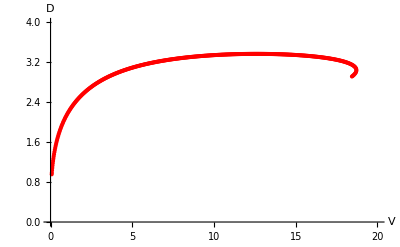

```mathematica
plotnumerique2=ListPlot[Data2[[All,{2,5}]],AxesLabel-> {Style["V",FontSize->22],Style["D",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotStyle->Red,PlotRange->{{0,20},{0,4}}]
```

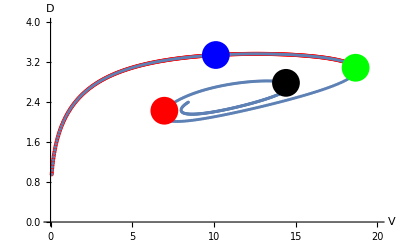

```mathematica
Show[plotnumerique2,plotnumerique,plotdot2,AxesStyle->Black,Epilog->{PointSize[0.05],Riffle[{Blue,Green,Red,Black},Point/@Datadots]},PlotRange->{{0,20},{0,4}}]
```

```mathematica
|
```

```mathematica
listeGRS[[325]]
```

{0.1,6.96323,-0.355988,-3.43422,2.23051,4.86882}